```mathematica
hessian[x1_,x2_]:={{12 x1^2+2(x2-1)^2+2(x2+1)^2  ,2x1(2x2-2)+2x1(2x2+2)},{2x1(2x2-2)+2x1(2x2+2),  4 x1^2+2(x2-1)^2+2(x2+1)^2+2*(2x2-2)*(2x2+2)}}
```

```mathematica
(*hessian[x1,y1]//TeXForm*)
```

```mathematica
xVector[x1_,x2_]:=Transpose[{x1,x2}]
```

```mathematica
grad[x1_,x2_]:={4x1*(1+x1^2+x2^2),4x2*(-1+x1^2+x2^2)}
```

```mathematica
b[x1_,x2_,x10_,x20_]:=grad[x10,x20]-hessian[x10,x20].xVector[x1-x10,x2-x20]
```

```mathematica
fFunc[x1_,x2_]:=(x1^2+(x2+1)^2)*(x1^2+(x2-1)^2)
```

```mathematica
gFunc[x1_,x2_,x10_,x20_]:=fFunc[x10,x20]+ 1/2*Transpose[xVector[x1-x10,x2-x20]].hessian[x10,x20].xVector[x1-x10,x2-x20]+Transpose[b[x10,x20]].xVector[x1-x10,x2-x20]
```

```mathematica
Show[Plot3D[{fFunc[x1,x2],gFunc[x1,x2,1/2,0]},{x1,-1.5,1.5},{x2,-1.5,1.5}, Mesh->None],Graphics3D[{Red,PointSize[0.05],Point[{1/2,0,0}]}],Graphics3D[{Green,PointSize[0.05],Point[{9/14,0,0}]}]]
```

-Graphics3D-

```mathematica
gFunc[x1,x2,1/2,0]
```

33/16-x1+1/2 (7 (-1/2+x1)^2-3 x2^2)

```mathematica
33/16-x1+1/2 (7 (-1/2+x1)^2-3 x2^2)//Expand
```

47/16-(9 x1)/2+(7 x1^2)/2-(3 x2^2)/2

#### Исследую на выпуклость

```mathematica
gFunc[x1,x2,1/2+d,0+d]
```

```mathematica
((-1+d)^2+(1/2+d)^2) ((1/2+d)^2+(1+d)^2)+(4 (1/2+d) (1+d^2+(1/2+d)^2)-(1/2+d) (2 (-1+d)^2+12 (1/2+d)^2+2 (1+d)^2)-d (2 (1/2+d) (-2+2 d)+2 (1/2+d) (2+2 d))) (-1/2-d+x1)+(4 d (-1+d^2+(1/2+d)^2)-(1/2+d) (2 (1/2+d) (-2+2 d)+2 (1/2+d) (2+2 d))-d (2 (-1+d)^2+4 (1/2+d)^2+2 (1+d)^2+2 (-2+2 d) (2+2 d))) (-d+x2)+1/2 ((-1/2-d+x1) ((2 (-1+d)^2+12 (1/2+d)^2+2 (1+d)^2) (-1/2-d+x1)+(2 (1/2+d) (-2+2 d)+2 (1/2+d) (2+2 d)) (-d+x2))+(-d+x2) ((2 (1/2+d) (-2+2 d)+2 (1/2+d) (2+2 d)) (-1/2-d+x1)+(2 (-1+d)^2+4 (1/2+d)^2+2 (1+d)^2+2 (-2+2 d) (2+2 d)) (-d+x2)))//Expand
```

47/16+(23 d)/2+30 d^2+60 d^3+60 d^4-(9 x1)/2-19 d x1-40 d^2 x1-40 d^3 x1+(7 x1^2)/2+6 d x1^2+8 d^2 x1^2-d x2-20 d^2 x2-40 d^3 x2+4 d x1 x2+8 d^2 x1 x2-(3 x2^2)/2+2 d x2^2+8 d^2 x2^2

```mathematica
(7 x1^2)/2+6 d x1^2+8 d^2 x1^2+4 d x1 x2+8 d^2 x1 x2-(3 x2^2)/2+2 d x2^2+8 d^2 x2^2 =x2^2(8d^2+2d-3/2) +x1^2(8d^2+6d+7/2)+x1*x2(8d^2+4d)
```

```mathematica
aMatrix = {{(8d^2+6d+7/2),(8d^2+4d)},{(8d^2+4d),(8d^2+2d-3/2)}};
```

```mathematica
aMatrix//MatrixForm
```

(7/2+6 d+8 d^2 | 4 d+8 d^2
4 d+8 d^2 | -3/2+2 d+8 d^2)

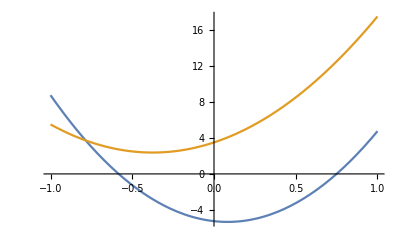

```mathematica
Plot[{Det[aMatrix],aMatrix[[1,1]]},{d,-1,1}]
```

существует неопределенность в выпуклости - второй минор матрицы A функции g(x) отрицателен в области стартовой точки

```mathematica
Plot3D[{gFunc[x1,x2,1/2,0]},{x1,-3,3+1/2},{x2,-3,3}]
```

-Graphics3D-

```mathematica
gFunc[1/2,0,1/2,0]
fFunc[1/2,0]
```

25/16

25/16

#### Стационарные точки g(x1, x2)

```mathematica
g[x1_,x2_]:=47/16-(9 x1)/2+(7 x1^2)/2-(3 x2^2)/2
```

```mathematica
Subscript[(g'), x1]=-9/2+7x1
Subscript[(g'), x2]=-3x2
```

Кандидат на стационарную точку - x_st(9/14, 0)

```mathematica
Subscript[H, g](Subscript[x1, st],Subscript[x2, st])={{7,0},{0,-3}};
Det[Subscript[H, g]] = -21
```

Найденная точка - седловая, не является экстремумом

```mathematica
D[gFunc[x1,x2,x10,x20],x1]
```

```mathematica
4 x10 (1+x10^2+x20^2)-x10 (12 x10^2+2 (-1+x20)^2+2 (1+x20)^2)-x20 (2 x10 (-2+2 x20)+2 x10 (2+2 x20))+1/2 (2 (x1-x10) (12 x10^2+2 (-1+x20)^2+2 (1+x20)^2)+2 (x2-x20) (2 x10 (-2+2 x20)+2 x10 (2+2 x20)))//FullSimplify
```

4 x1 (1+3 x10^2+x20^2)-4 x10 (1+5 x10^2-2 x2 x20+5 x20^2)

```mathematica
D[gFunc[x1,x2,x10,x20],x2]
```

```mathematica
4 x20 (-1+x10^2+x20^2)-x10 (2 x10 (-2+2 x20)+2 x10 (2+2 x20))-x20 (4 x10^2+2 (-1+x20)^2+2 (1+x20)^2+2 (-2+2 x20) (2+2 x20))+1/2 (2 (x1-x10) (2 x10 (-2+2 x20)+2 x10 (2+2 x20))+2 (x2-x20) (4 x10^2+2 (-1+x20)^2+2 (1+x20)^2+2 (-2+2 x20) (2+2 x20)))//FullSimplify
```

4 (x20+2 x1 x10 x20-5 x20 (x10^2+x20^2)+x2 (-1+x10^2+3 x20^2))